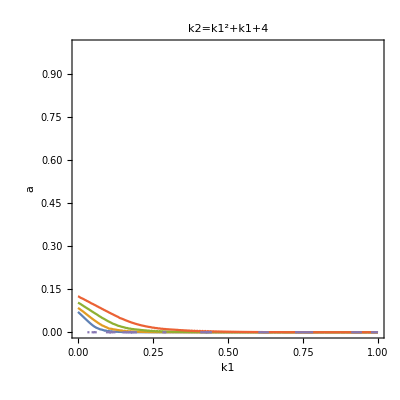

-Graphics3D-

```mathematica
k2=t=1;
m=((1-Abs[a]^2)^(-1))*{{(k2*Abs[a])^2-k1*k2, Conjugate[a]*(k1*k2-k2^2)},{a*(k1*k2-k1^2),(k1*Abs[a])^2-k1*k2}};
m3=m.m.m;
tracem3=Tr[m3];
determ3=Det[m3];
q=tracem3^2-4*determ3;
em3=Eigenvalues[m3];
ContourPlot[{q==1,q==.1,q==0.001,q==0.00001,q==0},{k1,0,1},{a,0,1},Contours->true,FrameLabel->Automatic];
Show[ContourPlot[{q==1,q==10,q==100,q==1000,q==0},{k1,0,1},{a,0,1},Contours->true,FrameLabel->Automatic],PlotLabel->HoldForm[k2=k1^2+k1+4],LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0],Italic}]
Show[Plot3D[em3,{k1,0,1},{a,0,1},AxesLabel->Automatic],PlotLabel->HoldForm[Eigenvalues for k2=k1^2+k1+4]]
```

```mathematica
Show[Show[Plot3D[em3,{k1,0,1},{a,0,1}],PlotLabel->HoldForm[Eigenvalues for k2=k1^2]]]
```